# Quest_07: Sequences.

1.Calculate the limit of the sequence          ((2n+1)/(2n-√n))^(√(n+2)) when n tends to infinity  .

```mathematica
Limit[((2n+1)/(2n-√n))^(√(n+2)),n-> Infinity]
```

√ⅇ

2 .	Calculating the limits, compare the order of magnitude of the sequences:  a_n=√(n^5)-√(n^3+1) and  b_n=log(n)

```mathematica
Limit[(√(n^5)-√(n^3+1))/(Log[n]),n-> Infinity]
```

∞

The limit of the quotient a_n/b_n =     ∞
          Therefore we can conclude that     √(n^5)-√(n^3+1))>>(Log[n]

3. 	Solve the recurrence:
                               a_1    = 1
                               a_(n+1) =a_n  √5 n≥1
and find   a_15

```mathematica
RSolve[{a[n+1]==a[n]  √5, a[1]==1},a[n],n]
```

{{a[n]→5^(-1/2+n/2)}}

```mathematica
%/.n->15
```

{{a[15]→78125}}

a_n=     5^(-1/2+n/2)               
           a_15=78125

4. 	Obtain the 10th first terms of the above sequence and do the plot of the obtained terms.

```mathematica
List1=Table[5^(-1/2+n/2)     ,{n,1,10}]
```

{1,√5,5,5 √5,25,25 √5,125,125 √5,625,625 √5}

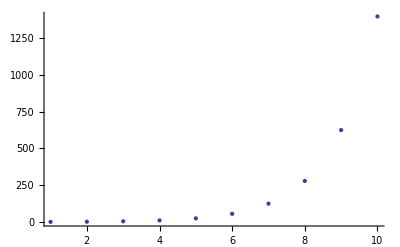

```mathematica
ListPlot[List1]
```